# Tension of the E_G statistic and RSD data with Planck/ΛCDM and implications for weakening gravity. Numerical Analysis and Construction Figures File

## Setting the Directory

```mathematica
(*                The runtime of the program is quite long   (~ 30 min for figs. 1,2,3,4,5,10   and  ~ 5 h for fig. 6)                 *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
(* In order to use the Needs["ErrorBarLogPlots`"] command you need to install the "Error Bar Log Plots" package which can be installed directly from the zip file "ErrorBarLogPlots.zip" or you can download it from http://library.wolfram.com/infocenter/MathSource/6747/*)

Needs["ErrorBarLogPlots`"]
Off[General::"obspkg",NIntegrate::"inumr",NIntegrate::ncvb,CompiledFunction::cflist,ListInterpolation::inhr,FindMinimum::lstol,Part::partw,NonlinearModelFit::cvmit];
```

## Parameter values

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"] 

(* Planck parameter Values for Planck18 *)

ompl=0.3153;
nn=2;
mm=2 ;
omplerr=0.0073;
h0pl=0.6727;
h0plerr=0.0066;
σ8pl=0.8111;
σ8plerr=0.006;
```

## Datasets

```mathematica
(* Data fσ8  *)

datafσ8={{0.35,0.44,0.05},{0.77,0.49,0.18},{0.17,0.51,0.06},{0.02,0.314,0.048},{0.02,0.398,0.065},{0.25,0.3512,0.0583},{0.37,0.4602,0.0378},{0.25,0.3665,0.0601},{0.37,0.4031,0.0586},{0.44,0.413,0.08},{0.6,0.39,0.063},{0.73,0.437,0.072},{0.067,0.423,0.055},{0.3,0.407,0.055},{0.4,0.419,0.041},{0.5,0.427,0.043},{0.6,0.433,0.067},{0.8,0.47,0.08},{0.35,0.429,0.089},{0.18,0.36,0.09},{0.38,0.44,0.06},{0.32,0.384,0.095},{0.32,0.48,0.1},{0.57,0.417,0.045},{0.15,0.49,0.145},{0.1,0.37,0.13},{1.4,0.482,0.116},{0.59,0.488,0.06},{0.38,0.497,0.045},{0.51,0.458,0.038},{0.61,0.436,0.034},{0.38,0.477,0.051},{0.51,0.453,0.05},{0.61,0.41,0.044},{0.76,0.44,0.04},{1.05,0.28,0.08},{0.32,0.427,0.056},{0.57,0.426,0.029},{0.727,0.296,0.0765},{0.02,0.428,0.0465},{0.6,0.55,0.12},{0.86,0.4,0.11},{0.1,0.48,0.16},{0.001,0.505,0.085},{0.85,0.45,0.11},{0.31,0.384,0.083},{0.36,0.409,0.098},{0.4,0.461,0.086},{0.44,0.426,0.062},{0.48,0.458,0.063},{0.52,0.483,0.075},{0.56,0.472,0.063},{0.59,0.452,0.061},{0.64,0.379,0.054}, {0.1,0.376,0.038},{1.52,0.42,0.076},{1.52,0.396,0.079},{0.978,0.379,0.176},{1.23,0.385,0.099},{1.526,0.342,0.07},{1.944,0.364,0.106},{0.60,0.49,0.12},{0.86,0.46,0.09},{0.57,0.501,0.051},{0.03,0.404,0.0815},{0.72,0.454,0.139}} ;
```

```mathematica
(* Data fσ8 with fiducial cosmology *)

datafσ8fid={{0.35,0.44,0.05,0.25},{0.77,0.49,0.18,0.25},{0.17,0.51,0.06,0.3},{0.02,0.314,0.048,0.266},{0.02,0.398,0.065,0.3},{0.25,0.3512,0.0583,0.25},{0.37,0.4602,0.0378,0.25},{0.25,0.3665,0.0601,0.25},{0.37,0.4031,0.0586,0.25},{0.44,0.413,0.08,0.27},{0.6,0.39,0.063,0.27},{0.73,0.437,0.072,0.27},{0.067,0.423,0.055,0.27},{0.3,0.407,0.055,0.25},{0.4,0.419,0.041,0.25},{0.5,0.427,0.043,0.25},{0.6,0.433,0.067,0.25},{0.8,0.47,0.08,0.25},{0.35,0.429,0.089,0.25},{0.18,0.36,0.09,0.27},{0.38,0.44,0.06,0.27},{0.32,0.384,0.095,0.274},{0.32,0.48,0.1,0.274},{0.57,0.417,0.045,0.274},{0.15,0.49,0.145,0.31},{0.1,0.37,0.13,0.3},{1.4,0.482,0.116,0.27},{0.59,0.488,0.06,0.307115},{0.38,0.497,0.045,0.31},{0.51,0.458,0.038,0.31},{0.61,0.436,0.034,0.31},{0.38,0.477,0.051,0.31},{0.51,0.453,0.05,0.31},{0.61,0.41,0.044,0.31},{0.76,0.44,0.04,0.308},{1.05,0.28,0.08,0.308},{0.32,0.427,0.056,0.31},{0.57,0.426,0.029,0.31},{0.727,0.296,0.0765,0.31},{0.02,0.428,0.0465,0.3},{0.6,0.55,0.12,0.3},{0.86,0.4,0.11,0.3},{0.1,0.48,0.16,0.25},{0.001,0.505,0.085,0.31},{0.85,0.45,0.11,0.3},{0.31,0.384,0.083,0.307},{0.36,0.409,0.098,0.307},{0.4,0.461,0.086,0.307},{0.44,0.426,0.062,0.307},{0.48,0.458,0.063,0.307},{0.52,0.483,0.075,0.307},{0.56,0.472,0.063,0.307},{0.59,0.452,0.061,0.307},{0.64,0.379,0.054,0.307},     {0.1,0.376,0.038,0.282},{1.52,0.42,0.076,0.26479},{1.52,0.396,0.079,0.31},{0.978,0.379,0.176,0.31},{1.23,0.385,0.099,0.31},{1.526,0.342,0.07,0.31},{1.944,0.364,0.106,0.31},{0.60,0.49,0.12,0.31},{0.86,0.46,0.09,0.31},{0.57,0.501,0.051,0.307},{0.03,0.404,0.0815,0.3121},{0.72,0.454,0.139,0.31}} ;
```

```mathematica
(* Subset of Data fσ8  *)

datafσ8sub={{0.02,0.314,0.048},{0.25,0.3512,0.0583},{0.44,0.413,0.08},{0.6,0.39,0.063},{0.73,0.437,0.072},{0.18,0.36,0.09},{0.15,0.49,0.145},{0.1,0.37,0.13},{1.4,0.482,0.116},{0.38,0.497,0.045},{0.51,0.458,0.038},{0.61,0.436,0.034},{1.05,0.28,0.08},{0.32,0.427,0.056},{0.727,0.296,0.0765},{0.02,0.428,0.0465},{0.001,0.505,0.085},{0.31,0.384,0.083},{0.36,0.409,0.098},{0.4,0.461,0.086},{0.44,0.426,0.062},{0.48,0.458,0.063},{0.52,0.483,0.075},{0.56,0.472,0.063},{0.59,0.452,0.061},{0.64,0.379,0.054},{0.978,0.379,0.176},{1.23,0.385,0.099},{1.526,0.342,0.07},{1.944,0.364,0.106},{0.60,0.49,0.12},{0.86,0.46,0.09},{0.57,0.501,0.051},{0.03,0.404,0.0815},{0.72,0.454,0.139}} ;

(* Subset of Data fσ8 with fiducial cosmology *)

datafσ8fidsub={{0.02,0.314,0.048,0.266},{0.25,0.3512,0.0583,0.25},{0.44,0.413,0.08,0.27},{0.6,0.39,0.063,0.27},{0.73,0.437,0.072,0.27},{0.18,0.36,0.09,0.27},{0.15,0.49,0.145,0.31},{0.1,0.37,0.13,0.3},{1.4,0.482,0.116,0.27},{0.38,0.497,0.045,0.31},{0.51,0.458,0.038,0.31},{0.61,0.436,0.034,0.31},{1.05,0.28,0.08,0.308},{0.32,0.427,0.056,0.31},{0.727,0.296,0.0765,0.31},{0.02,0.428,0.0465,0.3},{0.001,0.505,0.085,0.31},{0.31,0.384,0.083,0.307},{0.36,0.409,0.098,0.307},{0.4,0.461,0.086,0.307},{0.44,0.426,0.062,0.307},{0.48,0.458,0.063,0.307},{0.52,0.483,0.075,0.307},{0.56,0.472,0.063,0.307},{0.59,0.452,0.061,0.307},{0.64,0.379,0.054,0.307},{0.978,0.379,0.176,0.31},{1.23,0.385,0.099,0.31},{1.526,0.342,0.07,0.31},{1.944,0.364,0.106,0.31},{0.60,0.49,0.12,0.31},{0.86,0.46,0.09,0.31},{0.57,0.501,0.051,0.307},{0.03,0.404,0.0815,0.3121},{0.72,0.454,0.139,0.31}} ;
```

```mathematica
(* Data Eg(R)  *)

dataAmon1={{5.016293205,0.250199203,0.162549801},{5.379129519,0.399203187,0.169322709},{5.580059222,0.094422311,0.182868526},{8.157153824,0.30438247,0.142231076},{8.574067794,0.412749004,0.149003984},{9.029054528,0.419521912,0.243824701},{13.23177951,0.494023904,0.162549801},{13.95120389,0.433067729,0.169322709},{14.76817851,0.155378486,0.176095618},{21.08819264,0.514342629,0.230278884},{22.75123522,0.331474104,0.230278884},{23.96447708,0.324701195,0.325099602},{35.52466828,0.338247012,0.298007968},{36.98275829,0.405976096,0.33187251},{39.00804186,0.324701195,0.386055777},{56.60353085,0.372111554,0.805976096}};
dataAmon2={{5.134275368,0.236198946,0.147849418},{5.697099576,0.195649429,0.194884991},{8.284810129,0.322477492,0.127644653},{9.192998989,0.275208608,0.174703557},{13.64963041,0.213847716,0.127667984},{14.98918707,0.468973704,0.2553593},{24.43987313,0.958390975,0.470379062},{22.02542486,0.226213219,0.134364021},{36.28796609,0.480429293,0.181422925},{39.84921902,0.84978453,0.571146245},{59.78620124,0.546503074,0.45022096}};

dataReyes={{2.456221644,0.287912088,0.230769231},{3.419498847,0.498901099,0.168131868},{4.648373103,0.505494505,0.121978022},{6.624905237,0.327472527,0.092307692},{9.850107113,0.347252747,0.079120879},{14.83288548,0.456043956,0.082417582},{22.10663117,0.436263736,0.095604396},{45.87760079,0.324175824,0.105494505}};

dataAlam={{2.173069973,0.387115377,0.155404249},{3.309489708,0.261878186,0.109800201},{4.995575129,0.462659523,0.092904714},{7.56693925,0.426952413,0.089530081},{11.38063894,0.352397961,0.086144287},{17.26511247,0.433244038,0.099661421},{25.99212515,0.433013357,0.116549466},{39.60074697,0.338181345,0.157100867}};

datadelaTorre1={{2.646156127,0.319402985,0.143283582},{4.171409139,0.205970149,0.155223881},{6.631488986,0.223880597,0.173134328},{10.44486654,0.014925373,0.202985075},{16.37570457,0.098507463,0.262686567}};

datadelaTorre2={{2.614461175,0.345689974,0.129374769},{4.155660483,0.066851646,0.123492416},{6.60538172,0.117425083,0.135257122},{10.42344137,0.009211987,0.164742878},{16.56795817,0.100961894,0.211801702}};

dataBlake1={{1.763659524,0.748484848,0.217171717},{2.236425725,0.713131313,0.156565657},{2.850437507,0.354545455,0.141414141},{3.568113659,0.304040404,0.116161616},{4.45936402,0.354545455,0.111111111},{5.657447465,0.288888889,0.101010101},{7.059866849,0.435353535,0.111111111},{8.944480893,0.455555556,0.116161616},{11.33218801,0.475757576,0.121212121},{14.34355012,0.556565657,0.121212121},{17.98503831,0.4,0.121212121},{22.21001152,0.374747475,0.146464646},{28.88952743,0.394949495,0.181818182},{36.15749232,0.354545455,0.191919192},{45.2611369,0.304040404,0.303030303}};

dataBlake2={{1.7,0.343602694,0.29040404},{2.2,0.314141414,0.172558923},{2.7,0.575084175,0.138888889},{3.4,0.431986532,0.113636364},{4.4,0.356228956,0.105218855},{5.5,0.301515152,0.096801347},{6.9,0.246801347,0.088383838},{8.8,0.284680135,0.084175084},{11.1,0.267845118,0.084175084},{13.9,0.297306397,0.07996633},{17.7,0.242592593,0.07996633},{21.9,0.251010101,0.092592593},{27.8,0.326767677,0.105218855},{34.8,0.419360269,0.143097643},{44.2,0.621380471,0.193602694}};

dataJullo={{2.220562728,0.27734375,0.1796875},{3.569925863,0.13671875,0.23828125},{5.647622353,0.16015625,0.19921875},{8.862928581,0.4921875,0.2890625},{14.13443819,0.6484375,0.2265625},{22.54134636,0.29296875,0.14453125},{35.37459313,0.40625,0.21875}};

dataSingh1={{3.614304108,0.371314741,0.103585657},{4.913127388,0.429083665,0.085657371},{6.603179244,0.502788845,0.079681275},{9.078721448,0.399203187,0.071713147},{12.20168343,0.373306773,0.061752988},{16.58643635,0.450996016,0.061752988},{22.54687825,0.32749004,0.049800797},{30.30271083,0.395219124,0.059760956},{41.19218363,0.447011952,0.069721116},{55.99485807,0.458964143,0.087649402},{76.98741774,0.341434263,0.107569721},{103.4700871,0.283665339,0.155378486}};

dataSingh2={{2.568995517,0.488397059,0.085183661},{3.407128752,0.369343902,0.092590936},{4.608134656,0.324327709,0.081497916},{6.123096501,0.405270974,0.081462132},{8.201868601,0.338050849,0.074108533},{11.00330788,0.433790771,0.096276681},{14.87257951,0.322109105,0.074090641},{19.75030742,0.340090533,0.122255819},{26.21676088,0.313628312,0.15553488},{35.44198703,0.220464833,0.188921293}};
```

```mathematica
(* Data  Eg(z)*)

dataeg={{0.267,0.43,0.13},{0.27,0.4,0.05},{0.27,0.46,0.085},{0.305,0.27,0.08},{0.32,0.4,0.09},{0.32,0.48,0.1},{0.32,0.39,0.06},{0.554,0.26,0.07},{0.57,0.31,0.06},{0.57,0.3,0.07},{0.57,0.24,0.06},{0.57,0.42,0.056},{0.57,0.39,0.05},{0.57,0.43,0.1},{0.6,0.16,0.09},{0.86,0.09,0.07}};

dataegb={{0.267,0.43,0.13},{0.272,0.4,0.05},{0.275,0.46,0.085},{0.305,0.27,0.08},{0.32,0.4,0.09},{0.325,0.48,0.1},{0.33,0.39,0.06},{0.554,0.26,0.07},{0.57,0.31,0.06},{0.575,0.3,0.07},{0.58,0.24,0.06},{0.585,0.42,0.056},{0.56,0.39,0.05},{0.565,0.43,0.1},{0.6,0.16,0.09},{0.86,0.09,0.07}};
```

```mathematica
(*  Eg(z,R) data *)

dataAmon1R={{0.29,5.016293205,0.250199203,0.162549801},{0.29,5.379129519,0.399203187,0.169322709},{0.29,5.580059222,0.094422311,0.182868526},{0.29,8.157153824,0.30438247,0.142231076},{0.29,8.574067794,0.412749004,0.149003984},{0.29,9.029054528,0.419521912,0.243824701},{0.29,13.23177951,0.494023904,0.162549801},{0.29,13.95120389,0.433067729,0.169322709},{0.29,14.76817851,0.155378486,0.176095618},{0.29,21.08819264,0.514342629,0.230278884},{0.29,22.75123522,0.331474104,0.230278884},{0.29,23.96447708,0.324701195,0.325099602},{0.29,35.52466828,0.338247012,0.298007968},{0.29,36.98275829,0.405976096,0.33187251},{0.29,39.00804186,0.324701195,0.386055777},{0.29,56.60353085,0.372111554,0.805976096}};
dataAmon2R={{0.57,5.134275368,0.236198946,0.147849418},{0.57,5.697099576,0.195649429,0.194884991},{0.57,8.284810129,0.322477492,0.127644653},{0.57,9.192998989,0.275208608,0.174703557},{0.57,13.64963041,0.213847716,0.127667984},{0.57,14.98918707,0.468973704,0.2553593},{0.57,24.43987313,0.958390975,0.470379062},{0.57,22.02542486,0.226213219,0.134364021},{0.57,36.28796609,0.480429293,0.181422925},{0.57,39.84921902,0.84978453,0.571146245},{0.57,59.78620124,0.546503074,0.45022096}};

dataReyesR={{0.32,2.456221644,0.287912088,0.230769231},{0.32,3.419498847,0.498901099,0.168131868},{0.32,4.648373103,0.505494505,0.121978022},{0.32,6.624905237,0.327472527,0.092307692},{0.32,9.850107113,0.347252747,0.079120879},{0.32,14.83288548,0.456043956,0.082417582},{0.32,22.10663117,0.436263736,0.095604396},{0.32,45.87760079,0.324175824,0.105494505}};

dataAlamR={{0.57,2.173069973,0.387115377,0.155404249},{0.57,3.309489708,0.261878186,0.109800201},{0.57,4.995575129,0.462659523,0.092904714},{0.57,7.56693925,0.426952413,0.089530081},{0.57,11.38063894,0.352397961,0.086144287},{0.57,17.26511247,0.433244038,0.099661421},{0.57,25.99212515,0.433013357,0.116549466},{0.57,39.60074697,0.338181345,0.157100867}};

datadelaTorre1R={{0.6,2.646156127,0.319402985,0.143283582},{0.6,4.171409139,0.205970149,0.155223881},{0.6,6.631488986,0.223880597,0.173134328},{0.6,10.44486654,0.014925373,0.202985075},{0.6,16.37570457,0.098507463,0.262686567}};

datadelaTorre2R={{0.95,2.614461175,0.345689974,0.129374769},{0.95,4.155660483,0.066851646,0.123492416},{0.95,6.60538172,0.117425083,0.135257122},{0.95,10.42344137,0.009211987,0.164742878},{0.95,16.56795817,0.100961894,0.211801702}};

dataBlake1R={{0.29,1.763659524,0.748484848,0.217171717},{0.29,2.236425725,0.713131313,0.156565657},{0.29,2.850437507,0.354545455,0.141414141},{0.29,3.568113659,0.304040404,0.116161616},{0.29,4.45936402,0.354545455,0.111111111},{0.29,5.657447465,0.288888889,0.101010101},{0.29,7.059866849,0.435353535,0.111111111},{0.29,8.944480893,0.455555556,0.116161616},{0.29,11.33218801,0.475757576,0.121212121},{0.29,14.34355012,0.556565657,0.121212121},{0.29,17.98503831,0.4,0.121212121},{0.29,22.21001152,0.374747475,0.146464646},{0.29,28.88952743,0.394949495,0.181818182},{0.29,36.15749232,0.354545455,0.191919192},{0.29,45.2611369,0.304040404,0.303030303}};

dataBlake2R={{0.57,1.7,0.343602694,0.29040404},{0.57,2.2,0.314141414,0.172558923},{0.57,2.7,0.575084175,0.138888889},{0.57,3.4,0.431986532,0.113636364},{0.57,4.4,0.356228956,0.105218855},{0.57,5.5,0.301515152,0.096801347},{0.57,6.9,0.246801347,0.088383838},{0.57,8.8,0.284680135,0.084175084},{0.57,11.1,0.267845118,0.084175084},{0.57,13.9,0.297306397,0.07996633},{0.57,17.7,0.242592593,0.07996633},{0.57,21.9,0.251010101,0.092592593},{0.57,27.8,0.326767677,0.105218855},{0.57,34.8,0.419360269,0.143097643},{0.57,44.2,0.621380471,0.193602694}};

dataJulloR={{0.57,2.220562728,0.27734375,0.1796875},{0.57,3.569925863,0.13671875,0.23828125},{0.57,5.647622353,0.16015625,0.19921875},{0.57,8.862928581,0.4921875,0.2890625},{0.57,14.13443819,0.6484375,0.2265625},{0.57,22.54134636,0.29296875,0.14453125},{0.57,35.37459313,0.40625,0.21875}};

dataSingh1R={{0.27,3.614304108,0.371314741,0.103585657},{0.27,4.913127388,0.429083665,0.085657371},{0.27,6.603179244,0.502788845,0.079681275},{0.27,9.078721448,0.399203187,0.071713147},{0.27,12.20168343,0.373306773,0.061752988},{0.27,16.58643635,0.450996016,0.061752988},{0.27,22.54687825,0.32749004,0.049800797},{0.27,30.30271083,0.395219124,0.059760956},{0.27,41.19218363,0.447011952,0.069721116},{0.27,55.99485807,0.458964143,0.087649402},{0.27,76.98741774,0.341434263,0.107569721},{0.27,103.4700871,0.283665339,0.155378486}};

dataSingh2R={{0.57,2.568995517,0.488397059,0.085183661},{0.57,3.407128752,0.369343902,0.092590936},{0.57,4.608134656,0.324327709,0.081497916},{0.57,6.123096501,0.405270974,0.081462132},{0.57,8.201868601,0.338050849,0.074108533},{0.57,11.00330788,0.433790771,0.096276681},{0.57,14.87257951,0.322109105,0.074090641},{0.57,19.75030742,0.340090533,0.122255819},{0.57,26.21676088,0.313628312,0.15553488},{0.57,35.44198703,0.220464833,0.188921293}};
```

```mathematica
(* Subset of Data  Eg(z)*)

dataegsub={{0.267,0.43,0.13},{0.305,0.27,0.08},{0.32,0.4,0.09},{0.554,0.26,0.07},{0.57,0.31,0.06},{0.57,0.3,0.07},{0.6,0.16,0.09},{0.86,0.09,0.07}};

dataegbsub={{0.267,0.43,0.13},{0.305,0.27,0.08},{0.32,0.4,0.09},{0.554,0.26,0.07},{0.57,0.31,0.06},{0.575,0.3,0.07},{0.6,0.16,0.09},{0.86,0.09,0.07}};
```

## Theoretical Expressions

```mathematica
(* The fσ8  and the Subscript[E, G] observables *)

H[a_,w_,om_]:=√(om a^-3+(1-om)a^(-3(1+w)))
dLh[a_,om_,w_]:=2/(a √om)(Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),1-1/om]-√a Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),(1-1/om)a^(-3w)])
amin=0.001;

Geff[a_,ga_,n_]:=1+ga(1-a)^n-ga(1-a)^(2n);
Gl[z_,gb_,m_]:=1+gb(z/(1+z))^m-gb(z/(1+z))^(2m);

dsol[om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ]:=(dsol[om,w,ga,n]=Module[{a},NDSolve[{-((3 om d[a] Geff[a,ga,n])/(2 a^5  H[a,w,om]^2))+d'[a] (3/a+D[H[a,w,om],a]/H[a,w,om])+d''[a]==0,d[amin]==amin,d'[amin]==1},d,{a,amin,1}][[1]]])

Da[a_,om_,w_,ga_,n_]:=d[a]/.dsol[om,w,ga,n]
fa[aa_,om_,w_,ga_,n_]:=a d'[a]/d[a]/.a->aa/.dsol[om,w,ga,n]

fσ8geff[a_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,om,w,ga,n])/Da[1,om,w,ga,n] fa[aa,om,w,ga,n]/.aa->a
fσ8z[z_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,om,w,ga,n])/Da[1,om,w,ga,n] fa[aa,om,w,ga,n]/.aa->1/(1+z)

ffz[z_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ]:=fa[aa,om,w,ga,n]/.aa->1/(1+z)

ratio1[z_,w_,om_,omfid_]:=((H[a,w,om] dLh[a,om,w])/(H[a,-1,omfid] dLh[a,omfid,-1]))^(-1)/.a->1/(1+z);



eg[z_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,gb_?NumberQ,n_?NumberQ,m_?NumberQ]:=(om   Gl[z,gb,m]) /ffz[z,om,w,ga,n]
```

```mathematica
(* Sigma Difference of terms*)

dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
nsig[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2}][[1,2]]
```

## Figure 1

```mathematica
(* Covariance Matrix for data  fσ8*)


Cijwigglez=10^-3*({{6.400, 2.570, 0.000}, {2.570, 3.969, 2.540}, {0.000, 2.540, 5.184}});

Wigglez={10,11,12};
Cijfσ8=DiagonalMatrix[datafσ8fid[[All,3]]^2];
Cijfσ8[[Wigglez,Wigglez]]=Cijwigglez;
InvCijfσ8=Inverse[Cijfσ8];
```

```mathematica
(* Correlated χ^2 term for fσ8 with fiducial cosmology *)

vecfσ8[data_,w_,om_,ga_,n_,σ8_]:=Table[data[[i,2]]-ratio1[data[[i,1]],w,om,data[[i,4]]]fσ8geff[1/(1+data[[i,1]]),om,w,ga,n,σ8],{i,1,Length[data]}]
chi2fid[data_,w_,om_,ga_,n_,σ8_]:=vecfσ8[data,w,om,ga,n,σ8].InvCijfσ8.vecfσ8[data,w,om,ga,n,σ8]
```

```mathematica
(* Correlated χ^2 term for fσ8 without fiducial cosmology *)

vecfσ8nofid[data_,w_,om_,ga_,n_,σ8_]:=Table[data[[i,2]]-fσ8geff[1/(1+data[[i,1]]),om,w,ga,n,σ8],{i,1,Length[data]}]
chi2nofid[data_,w_,om_,ga_,n_,σ8_]:=vecfσ8nofid[data,w,om,ga,n,σ8].InvCijfσ8.vecfσ8nofid[data,w,om,ga,n,σ8]
```

```mathematica
(* Minimization of χ^2 for data fσ8 with fiducial cosmology *)

chi2minfσ8=FindMinimum[chi2fid[datafσ8fid,-1,om,ga,2,σ8],{om,0.30,0.31},{ga,0,-1},{σ8,0.8,0.81}]
```

{32.0423,{om→0.272466,ga→-1.30663,σ8→0.885758}}

```mathematica
(* Minimization of χ^2 for data fσ8 without fiducial cosmology *)

chi2minfσ8nofid=FindMinimum[chi2nofid[datafσ8,-1,om,ga,2,σ8],{om,0.30,0.31},{ga,0,-1},{σ8,0.8,0.81}]
```

{32.2021,{om→0.26252,ga→-1.33146,σ8→0.903454}}

```mathematica
(* Tension level in the  3D parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8) with fiducial cosmology *)

dchifσ8omgaσ8=chi2fid[datafσ8fid,-1,ompl,0,2,σ8pl]-chi2minfσ8[[1]];
nsigfσ8omgaσ8[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,4}][[1,2]]
nsigfσ8omgaσ8[dchifσ8omgaσ8,3]
```

3.69556

```mathematica
(* Tension level in the  3D parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8) without fiducial cosmology *)

dchifσ8nofidomgaσ8=chi2nofid[datafσ8,-1,ompl,0,2,σ8pl]-chi2minfσ8nofid[[1]];

nsig[dchifσ8nofidomgaσ8,3]
```

4.14733

```mathematica
(* 1σ  standard deviations with fiducial cosmology*)

fσ8s1om=FindRoot[chi2fid[datafσ8fid,-1,om,chi2minfσ8[[2,2,2]],2,chi2minfσ8[[2,3,2]]]==chi2minfσ8[[1]]+1,{om,chi2minfσ8[[2,1,2]]+0.5}][[1,2]]-chi2minfσ8[[2,1,2]];
fσ8s1ga=FindRoot[chi2fid[datafσ8fid,-1,chi2minfσ8[[2,1,2]],ga,2,chi2minfσ8[[2,3,2]]]==chi2minfσ8[[1]]+1,{ga,chi2minfσ8[[2,2,2]]+0.5}][[1,2]]-chi2minfσ8[[2,2,2]];
fσ8s1σ8=FindRoot[chi2fid[datafσ8fid,-1,chi2minfσ8[[2,1,2]],chi2minfσ8[[2,2,2]],2,σ8]==chi2minfσ8[[1]]+1,{σ8,chi2minfσ8[[2,3,2]]+0.5}][[1,2]]-chi2minfσ8[[2,3,2]];

Print["1σ Ωm=",fσ8s1om]
Print["1σ ga=",fσ8s1ga]
Print["1σ σ8=",fσ8s1σ8]
```

1σ Ωm=0.018718

1σ ga=0.139569

1σ σ8=0.0154297

```mathematica
(* 1σ  standard deviations without fiducial cosmology*)

fσ8nofids1om=FindRoot[chi2nofid[datafσ8,-1,om,chi2minfσ8nofid[[2,2,2]],2,chi2minfσ8nofid[[2,3,2]]]==chi2minfσ8nofid[[1]]+1,{om,chi2minfσ8nofid[[2,1,2]]+0.5}][[1,2]]-chi2minfσ8nofid[[2,1,2]];
fσ8nofids1ga=FindRoot[chi2nofid[datafσ8,-1,chi2minfσ8nofid[[2,1,2]],ga,2,chi2minfσ8nofid[[2,3,2]]]==chi2minfσ8nofid[[1]]+1,{ga,chi2minfσ8nofid[[2,2,2]]+0.5}][[1,2]]-chi2minfσ8nofid[[2,2,2]];
fσ8nofids1σ8=FindRoot[chi2nofid[datafσ8,-1,chi2minfσ8nofid[[2,1,2]],chi2minfσ8nofid[[2,2,2]],2,σ8]==chi2minfσ8nofid[[1]]+1,{σ8,chi2minfσ8nofid[[2,3,2]]+0.5}][[1,2]]-chi2minfσ8nofid[[2,3,2]];

Print["1σ Ωm=",fσ8nofids1om]
Print["1σ ga=",fσ8nofids1ga]
Print["1σ σ8=",fσ8nofids1σ8]
```

1σ Ωm=0.0148414

1σ ga=0.137648

1σ σ8=0.0157383

```mathematica
(* Plot fs8(z) and  best fit on dataset with 1σ deviation *)

pldatafσ8=ErrorListPlot[datafσ8,Frame->True,FrameLabel->{"z","fσ_8(z)"},BaseStyle->FontSize->16,PlotRange->{{0,2},{0,0.7}},PlotStyle->{PointSize->Large,Darker[Green]},ImageSize->Large]; 

pldatafσ8sub=ErrorListPlot[datafσ8sub,Frame->True,FrameLabel->{"z","fσ_8(z)"},BaseStyle->FontSize->16,PlotRange->{{0,2},{0,0.7}},PlotStyle->{PointSize->Large,Darker[Red]},ImageSize->Large]; 

plotfσ8gr=Plot[  fσ8geff[1/(1+z),ompl,-1,0,2,σ8pl],{z,0,2},Frame->True,FrameLabel->{"z","fσ_8(z)"},BaseStyle->FontSize->18,PlotStyle->{PointSize->Large,Thick,Red},PlotRange->{{0,2},{0,0.7}},Axes->False,ImageSize->Large];

fσ8par={om,ga,σ8};
```

```mathematica
wfσ8[z_,om_,ga_,σ8_]:=fσ8geff[1/(1+z),om,-1,ga,2,σ8];
```

```mathematica
dfσ8[z_,om_,ga_,σ8_,k_]:=D[wfσ8[z,om,ga,σ8],fσ8par[[k]]];
```

```mathematica
sfσ8[z_,om_,ga_,σ8_,cijs_]:= √(Sum[dfσ8[z,om,ga,σ8,i]^2  cijs[[i,i]],{i,1,Length[fσ8par]}]+2Sum[dfσ8[z,om,ga,σ8,i]  dfσ8[z,om,ga,σ8,j]  cijs[[i,j]],{i,1,Length[fσ8par]},{j,i+1,Length[fσ8par]}]);
```

```mathematica
cijs={{fσ8s1om^2,fσ8s1om  fσ8s1ga,fσ8s1om  fσ8s1σ8},{fσ8s1om fσ8s1ga,fσ8s1ga^2,fσ8s1ga  fσ8s1σ8},{fσ8s1om  fσ8s1σ8,fσ8s1ga  fσ8s1σ8,fσ8s1σ8^2}}
```

{{0.000350363,0.00261245,0.000288812},{0.00261245,0.0194795,0.00215351},{0.000288812,0.00215351,0.000238075}}

```mathematica
fσ8bf=wfσ8[z,om,ga,σ8]/.chi2minfσ8[[2]];
```

```mathematica
fσ8bfs1=(wfσ8[z,om,ga,σ8]+sfσ8[z,om,ga,σ8,cijs])/.chi2minfσ8[[2]];
```

```mathematica
fσ8bfs2=(wfσ8[z,om,ga,σ8]-sfσ8[z,om,ga,σ8,cijs])/.chi2minfσ8[[2]];
```

```mathematica
ParallelEvaluate[Off[InterpolatingFunction::dmvalD];];Off[InterpolatingFunction::dmval];
```

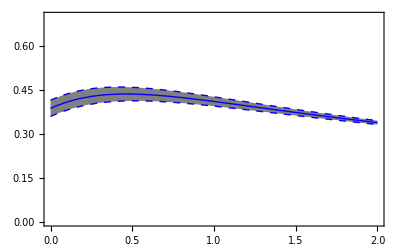

```mathematica
plfσ8bfs=Plot[{fσ8bfs1,fσ8bf,fσ8bfs2},{z,0,2},PlotRange->{{0,2},{0,0.7}},Filling->{{ 1->{{2},Gray}},{ 2->{{3},Gray}}},Frame->True,PlotStyle->{{PointSize->Large,Dashed,Thin,Blue},{PointSize->Large,Thick,Blue},{PointSize->Large,Dashed,Thin,Blue}},Axes->False]
```

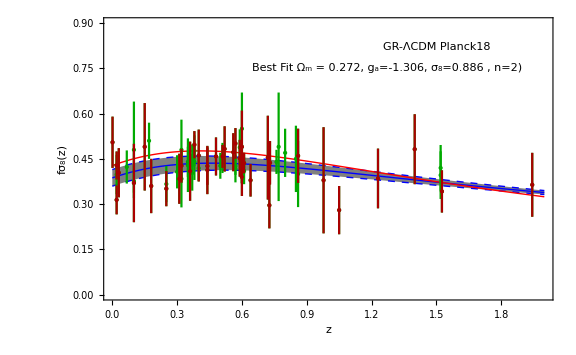

```mathematica
figfσ8zbfs=Show[plfσ8bfs,plotfσ8gr,pldatafσ8,pldatafσ8sub,Graphics[{Inset[" GR-ΛCDM Planck18",{1.5,0.82},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",16}]}],Graphics[{Inset[" Best Fit Ω_m = 0.272, g_a=-1.306, σ_8=0.886 , n=2) ",{1.27,0.75},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",16}]}],PlotRange->{{0,2},{0,0.9}},FrameLabel->{"z","fσ_8(z)"},BaseStyle->{FontFamily->"Times",16},FrameStyle->Directive[Black,Thick],ImageSize->Large]
Export[NotebookDirectory[]<>"figfs8zbfssub.pdf",figfσ8zbfs,ImageResolution->1000];
```

## Figure 3

```mathematica
(* Tension level in  2D projected space  (Subscript[Ω, 0m], Subscript[g, a]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8) with fiducial cosmology *)

dchifσ8omga=chi2fid[datafσ8fid,-1,ompl,0,2,chi2minfσ8[[2,3,2]]]-chi2minfσ8[[1]];
```

```mathematica
nsigfσ8omga[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,7}]
```

```mathematica
If[dchifσ8omga<76,nsigfσ8omga[dchifσ8omga,3],nsigfσ8omga>8.2]
```

nsigfσ8omga>8.2

```mathematica
(* Tension level in  2D projected space  (Subscript[Ω, 0m], Subscript[g, a]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8)  without fiducial cosmology *)

dchifσ8nofidomga=chi2nofid[datafσ8,-1,ompl,0,2,chi2minfσ8nofid[[2,3,2]]]-chi2minfσ8nofid[[1]];
nsigfσ8nofidomga[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,7}][[1,2]]
If[dchifσ8omga<76,nsigfσ8omga[dchifσ8omga,3],nsigfσ8omga>8.2]
```

nsigfσ8omga>8.2

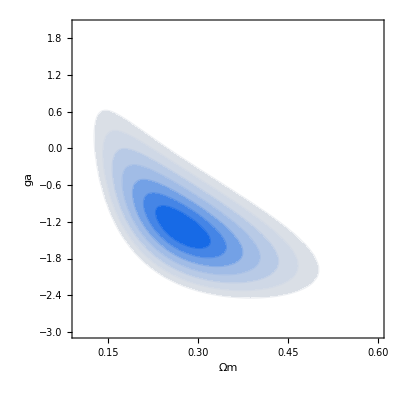

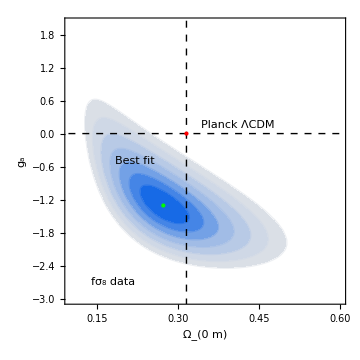

```mathematica
(* 1σ-7σ confidence contour in 2D projected space  (Subscript[Ω, 0m], Subscript[g, a]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8) including the fiducial correction factor*)

contour1fσ8=ContourPlot[chi2fid[datafσ8fid,-1,om,ga,2,chi2minfσ8[[2,3,2]]],{om,0.1,0.6},{ga,-3,2},FrameLabel->{"Ωm","ga"},Contours->{chi2minfσ8[[1]]+dchi[1,3],chi2minfσ8[[1]]+dchi[2,3],chi2minfσ8[[1]]+dchi[3,3],chi2minfσ8[[1]]+dchi[4,3],chi2minfσ8[[1]]+dchi[5,3],chi2minfσ8[[1]]+dchi[6,3],chi2minfσ8[[1]]+dchi[7,3]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White}]


cont1fσ8=Show[contour1fσ8,Graphics[{Inset["Best fit",{0.22,-0.5},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["fσ_8 data ",{0.18,-2.7},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.41,0.15},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","g_a"},PlotRange->{{0.1,0.6},{-3,2}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{0.3153,-6},{0.3153,3}}]},{Dashed,Line[{{-5,0},{5,0}}]},{PointSize[Large],Red,Point[{0.3153,0}]},{PointSize[Large],Green,Point[{chi2minfσ8[[2,1,2]],chi2minfσ8[[2,2,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

```mathematica
(* Tension level in  2D projected space  (Subscript[Ω, 0m], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8) with fiducial cosmology *)

dchifσ8omσ8=chi2fid[datafσ8fid,-1,ompl,chi2minfσ8[[2,2,2]],2,σ8pl]-chi2minfσ8[[1]];
nsigfσ8omσ8[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2}][[1,2]]
nsigfσ8omσ8[dchifσ8omσ8,3]
```

2.99504

```mathematica
(* Tension level in  2D projected space  (Subscript[Ω, 0m], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8) without fiducial cosmology *)

dchifσ8nofidomσ8=chi2nofid[datafσ8,-1,ompl,chi2minfσ8nofid[[2,2,2]],2,σ8pl]-chi2minfσ8nofid[[1]];
nsigfσ8nofidomσ8[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2}][[1,2]]
nsigfσ8nofidomσ8[dchifσ8nofidomσ8,3]
```

2.75337

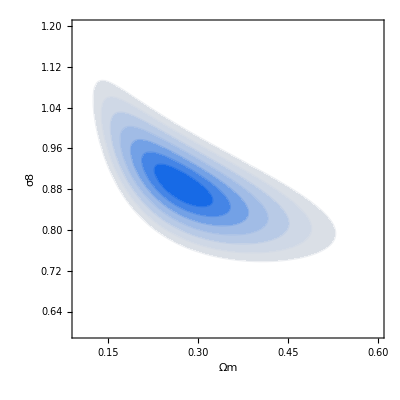

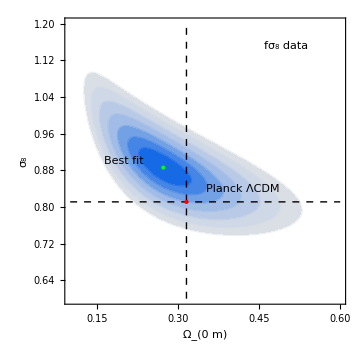

```mathematica
(* 1σ-7σ confidence contour in 2D projected space  (Subscript[Ω, 0m], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8) including the fiducial correction factor*)

contour2fσ8=ContourPlot[chi2fid[datafσ8fid,-1,om,chi2minfσ8[[2,2,2]],2,σ8],{om,0.1,0.6},{σ8,0.6,1.2},FrameLabel->{"Ωm","σ8"},Contours->{chi2minfσ8[[1]]+dchi[1,3],chi2minfσ8[[1]]+dchi[2,3],chi2minfσ8[[1]]+dchi[3,3],chi2minfσ8[[1]]+dchi[4,3],chi2minfσ8[[1]]+dchi[5,3],chi2minfσ8[[1]]+dchi[6,3],chi2minfσ8[[1]]+dchi[7,3]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White}]



cont2fσ8=Show[contour2fσ8,Graphics[{Inset["Best fit",{0.2,0.9},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["fσ_8 data ",{0.5,1.15},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.42,0.84},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0.1,0.6},{0.6,1.2}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{0.3153,0.6},{0.3153,1.2}}]},{Dashed,Line[{{0.1,0.8111},{0.6,0.8111}}]},{PointSize[Large],Red,Point[{0.3153,0.8111}]},{PointSize[Large],Green,Point[{chi2minfσ8[[2,1,2]],chi2minfσ8[[2,3,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

```mathematica
(* Tension level in  2D projected space  (Subscript[g, a], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8) with fiducial cosmology *)

dchifσ8σ8ga=chi2fid[datafσ8fid,-1,chi2minfσ8[[2,1,2]],0,2,σ8pl]-chi2minfσ8[[1]];
nsigfσ8σ8ga[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2}][[1,2]]
nsigfσ8σ8ga[dchifσ8σ8ga,3]
```

2.0752

```mathematica
(* Tension level in  2D projected space  (Subscript[g, a], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8) without fiducial cosmology *)


dchifσ8nofidσ8ga=chi2nofid[datafσ8,-1,chi2minfσ8nofid[[2,1,2]],0,2,σ8pl]-chi2minfσ8nofid[[1]];
nsigfσ8nofidσ8ga[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2}][[1,2]]
nsigfσ8nofidσ8ga[dchifσ8nofidσ8ga,3]
```

1.12544

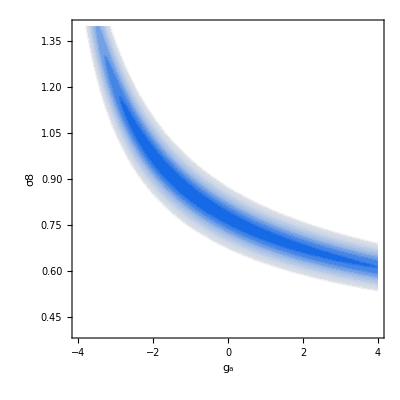

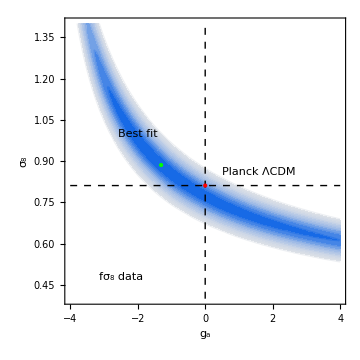

```mathematica
(* 1σ-7σ confidence contour in 2D projected space  (Subscript[g, a], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8) including the fiducial correction factor*)

contour3fσ8=ContourPlot[chi2fid[datafσ8fid,-1,chi2minfσ8[[2,1,2]],ga,2,σ8],{ga,-4,4},{σ8,0.4,1.4},FrameLabel->{"g_a","σ8"},Contours->{chi2minfσ8[[1]]+dchi[1,3],chi2minfσ8[[1]]+dchi[2,3],chi2minfσ8[[1]]+dchi[3,3],chi2minfσ8[[1]]+dchi[4,3],chi2minfσ8[[1]]+dchi[5,3],chi2minfσ8[[1]]+dchi[6,3],chi2minfσ8[[1]]+dchi[7,3]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White}]


cont3fσ8=Show[contour3fσ8,Graphics[{Inset["Best fit",{-2,1},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["fσ_8 data ",{-2.5,0.48},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{1.6,0.86},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"g_a","σ_8"},PlotRange->{{-4,4},{0.4,1.4}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{0,0.4},{0,1.4}}]},{Dashed,Line[{{-4,0.8111},{4,0.8111}}]},{PointSize[Large],Red,Point[{0,0.8111}]},{PointSize[Large],Green,Point[{chi2minfσ8[[2,2,2]],chi2minfσ8[[2,3,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

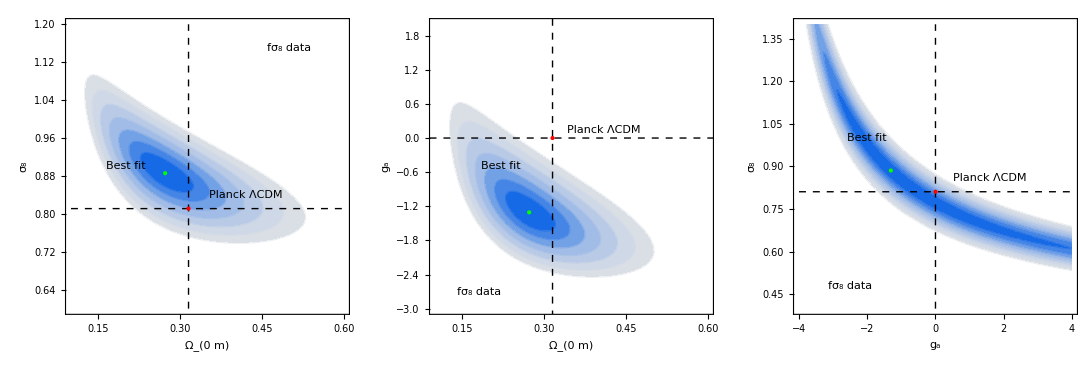

```mathematica
(* The three 1σ-7σ confidence contours in 2D projected spaces of the parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8) including the fiducial correction factor*)

figfσ8=GraphicsGrid[{{cont2fσ8,cont1fσ8,cont3fσ8}},Spacings->0]
Export[NotebookDirectory[]<>"fs8all.pdf",figfσ8,ImageResolution->1000];
```

## Figure 10

```mathematica
(* Covariance Matrix for data  Eg*)

Cijeg=DiagonalMatrix[dataeg[[All,3]]^2];
InvCijeg=Inverse[Cijeg];
Cijeg//MatrixForm;
```

```mathematica
(* Correlated χ^2 term for Eg*)

veceg[data_,w_,om_,ga_,gb_,n_,m_]:=Table[(data[[i,2]]-eg[data[[i,1]],om,w,ga,gb,n,m]),{i,1,Length[data]}];
chi2eg[data_,w_,om_,ga_,gb_,n_,m_]:=veceg[data,w,om,ga,gb,n,m].InvCijeg.veceg[data,w,om,ga,gb,n,m]
```

```mathematica
(* Minimization of χ^2 for data Eg*)

ParallelEvaluate[On[InterpolatingFunction::dmvalD];];On[InterpolatingFunction::dmval];
```

```mathematica
chi2mineg=FindMinimum[chi2eg[dataeg,-1,om,ga,gb,2,2],{om,0.31},{ga,0},{gb,0}]
```

{21.1404,{om→0.312923,ga→-0.1295,gb→-2.30782}}

```mathematica
(* Plot Eg(R) *)

dataAmon1err=ErrorListLogLinearPlot[dataAmon1,Frame->True,BaseStyle->FontSize->16,PlotStyle->{PointSize->Large,Red},PlotRange->{{1,150},{-1,2}},ImageSize->Large];

dataAmon2err=ErrorListLogLinearPlot[dataAmon2,Frame->True,BaseStyle->FontSize->16,PlotStyle->{PointSize->Large,Darker[Blue]},PlotRange->{{1,150},{-1,2}},ImageSize->Large];

dataReyeserr=ErrorListLogLinearPlot[dataReyes,Frame->True,BaseStyle->FontSize->16,PlotStyle->{PointSize->Large,Green},PlotRange->{{1,150},{-1,2}},ImageSize->Large];

dataAlamerr=ErrorListLogLinearPlot[dataAlam,Frame->True,BaseStyle->FontSize->16,PlotStyle->{PointSize->Large,Orange},PlotRange->{{1,150},{-1,2}},ImageSize->Large];
datadelaTorreerr1=ErrorListLogLinearPlot[datadelaTorre1,Frame->True,BaseStyle->FontSize->16,PlotStyle->{PointSize->Large,Magenta},PlotRange->{{1,150},{-1,2}},ImageSize->Large];

datadelaTorreerr2=ErrorListLogLinearPlot[datadelaTorre2,Frame->True,BaseStyle->FontSize->16,PlotStyle->{PointSize->Large,Darker[Yellow]},PlotRange->{{1,150},{-1,2}},ImageSize->Large];

dataBlakeerr1=ErrorListLogLinearPlot[dataBlake1,Frame->True,BaseStyle->FontSize->16,PlotStyle->{PointSize->Large,Darker[Magenta]},PlotRange->{{1,150},{-1,2}},ImageSize->Large];

dataBlakeerr2=ErrorListLogLinearPlot[dataBlake2,Frame->True,BaseStyle->FontSize->16,PlotStyle->{PointSize->Large,Darker[Red]},PlotRange->{{1,150},{-1,2}},ImageSize->Large];

dataJulloerr=ErrorListLogLinearPlot[dataJullo,Frame->True,BaseStyle->FontSize->16,PlotStyle->{PointSize->Large,Darker[Green]},PlotRange->{{1,150},{-1,2}},ImageSize->Large];

dataSingherr1=ErrorListLogLinearPlot[dataSingh1,Frame->True,BaseStyle->FontSize->16,PlotStyle->{PointSize->Large,Lighter[Blue]},PlotRange->{{1,150},{-1,2}},ImageSize->Large];

dataSingherr2=ErrorListLogLinearPlot[dataSingh2,Frame->True,BaseStyle->FontSize->16,PlotStyle->{PointSize->Large,Lighter[Red]},PlotRange->{{1,150},{-1,2}},ImageSize->Large];
```

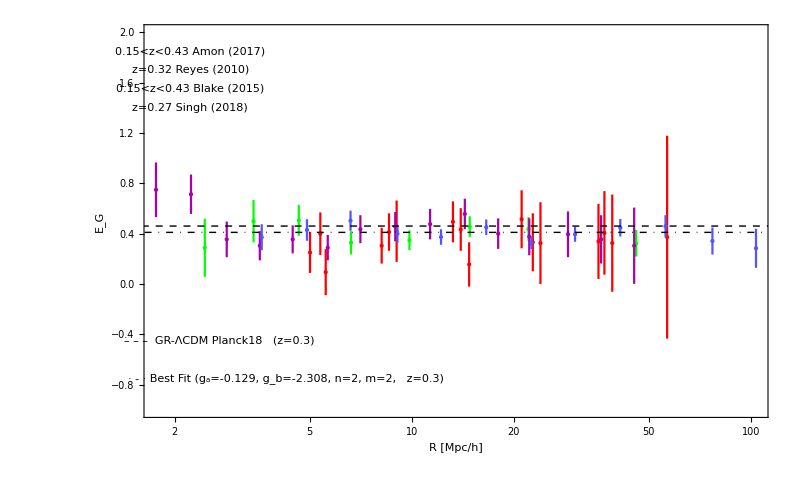

```mathematica
figerr1=Show[dataAmon1err,dataReyeserr,dataBlakeerr1,dataSingherr1,Graphics[{Inset["0.15<z<0.43 Amon (2017)",{0.8,1.85},BaseStyle->Directive[Bold,Red,Italic,FontFamily->"Times",16]]}],Graphics[{Inset["z=0.32 Reyes (2010)",{0.8,1.7},BaseStyle->Directive[Bold,Green,Italic,FontFamily->"Times",16]]}],Graphics[{Inset["0.15<z<0.43 Blake (2015)",{0.8,1.55},BaseStyle->Directive[Bold,Darker[Magenta],Italic,FontFamily->"Times",16]]}],Graphics[{Inset["z=0.27 Singh (2018)",{0.8,1.4},BaseStyle->Directive[Bold,Lighter[Blue],Italic,FontFamily->"Times",16]]}], Graphics[{Inset["– – –  GR-ΛCDM Planck18   (z=0.3)",{1,-0.45},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],Graphics[{Inset["· - · Best Fit (g_a=-0.129, g_b=-2.308, n=2, m=2,   z=0.3)",{1.45,-0.75},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],
Epilog->{{Dashed,Line[{{0,eg[0.3,ompl,-1,0,0,2,2]},{100,eg[0.3,ompl,-1,0,0,2,2]}}],Thickness[0.28]},{DotDashed,Line[{{0,eg[0.3,0.313,-1,-0.129,-2.308,2,2]},{100,eg[0.3,0.313,-1,-0.129,-2.308,2,2]}}],Thickness[0.28]}},FrameLabel->{"R [Mpc/h]","E_G"},Axes->None,PlotRange->{-1,2},ImageSize->800,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],FrameStyle->Directive[Black,Thick]]
```

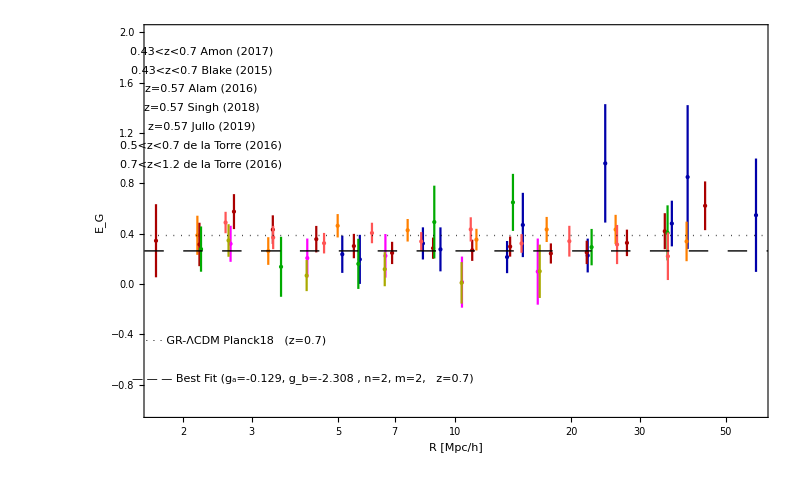

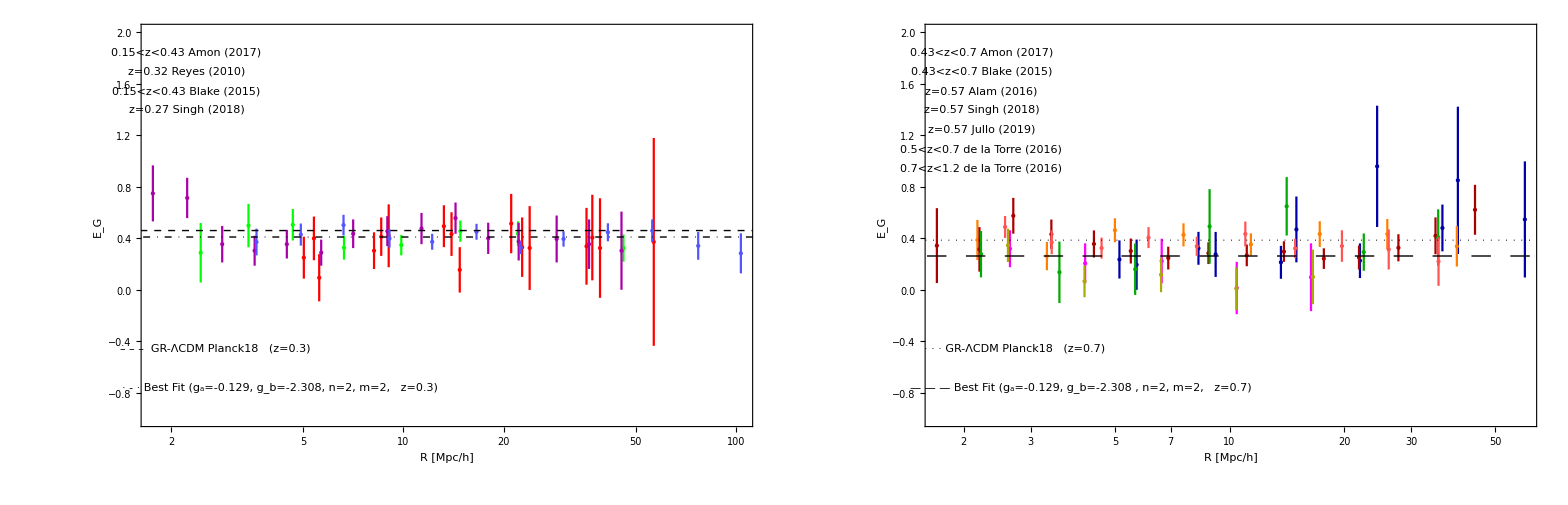

```mathematica
figerr2=Show[dataAmon2err,dataAlamerr,datadelaTorreerr1,datadelaTorreerr2,dataBlakeerr2,dataJulloerr,dataSingherr2, Graphics[{Inset["0.43<z<0.7 Amon (2017)",{0.8,1.85},BaseStyle->Directive[Bold,Darker[Blue],Italic,FontFamily->"Times",16]]}],Graphics[{Inset["z=0.57 Alam (2016)",{0.8,1.55},BaseStyle->Directive[Bold,Orange,Italic,FontFamily->"Times",16]]}],Graphics[{Inset["0.5<z<0.7 de la Torre (2016)",{0.8,1.1},BaseStyle->Directive[Bold,Magenta,Italic,FontFamily->"Times",16]]}],Graphics[{Inset["0.7<z<1.2 de la Torre (2016)",{0.8,0.95},BaseStyle->Directive[Bold,Darker[Yellow],Italic,FontFamily->"Times",16]]}],Graphics[{Inset["0.43<z<0.7 Blake (2015)",{0.8,1.7},BaseStyle->Directive[Bold,Darker[Red],Italic,FontFamily->"Times",16]]}],Graphics[{Inset["z=0.57 Jullo (2019)",{0.8,1.25},BaseStyle->Directive[Bold,Darker[Green],Italic,FontFamily->"Times",16]]}],Graphics[{Inset["z=0.57 Singh (2018)",{0.8,1.4},BaseStyle->Directive[Bold,Lighter[Red],Italic,FontFamily->"Times",16]]}],Graphics[{Inset["· · · GR-ΛCDM Planck18   (z=0.7)",{1,-0.45},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],Graphics[{Inset["— — — Best Fit (g_a=-0.129, g_b=-2.308 , n=2, m=2,   z=0.7)",{1.4,-0.75},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],
Epilog->{{Dotted,Line[{{0,eg[0.7,ompl,-1,0,0,2,2]},{100,eg[0.7,ompl,-1,0,0,2,2]}}],Thickness[0.28]},{Dashing[Large],Line[{{0,eg[0.7,0.313,-1,-0.129,-2.308,2,2]},{100,eg[0.7,0.313,-1,-0.129,-2.308,2,2]}}],Thickness[0.28]}},FrameLabel->{"R [Mpc/h]","E_G"},Axes->None,PlotRange->{-1,2},ImageSize->800,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],FrameStyle->Directive[Black,Thick]] 

figerr=GraphicsGrid[{{figerr1,figerr2}},Spacings->0]


Export[NotebookDirectory[]<>"figEgRerr2.pdf",figerr,ImageResolution->1000];
```

## Figure 2

```mathematica
(* Tension level in the  3D parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b] )  *)

dchieggagbom=chi2eg[dataeg,-1,ompl,0,0,2,2]-chi2mineg[[1]];
nsigeggagbom[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,3}][[1,2]];
nsigeggagbom[dchieggagbom,3]
```

4.57612

```mathematica
(* 1σ  standard deviations  *)

egs1om=FindRoot[chi2eg[dataeg,-1,om,chi2mineg[[2,2,2]],chi2mineg[[2,3,2]],2,2]==chi2mineg[[1]]+1,{om,chi2mineg[[2,1,2]]+0.5}][[1,2]]-chi2mineg[[2,1,2]];
egs1ga=FindRoot[chi2eg[dataeg,-1,chi2mineg[[2,1,2]],ga,chi2mineg[[2,3,2]],2,2]==chi2mineg[[1]]+1,{ga,chi2mineg[[2,2,2]]+0.5}][[1,2]]-chi2mineg[[2,2,2]];
egs1gb=FindRoot[chi2eg[dataeg,-1,chi2mineg[[2,1,2]],chi2mineg[[2,2,2]],gb,2,2]==chi2mineg[[1]]+1,{gb,chi2mineg[[2,3,2]]+0.5}][[1,2]]-chi2mineg[[2,3,2]];

Print["1σ Ωm=",egs1om]
Print["1σ ga=",egs1ga]
Print["1σ gb=",egs1gb]
```

1σ Ωm=0.0243368

1σ ga=0.490402

1σ gb=0.422686

{{0.000592282,0.0119348,0.0102868},{0.0119348,0.240494,0.207286},{0.0102868,0.207286,0.178664}}

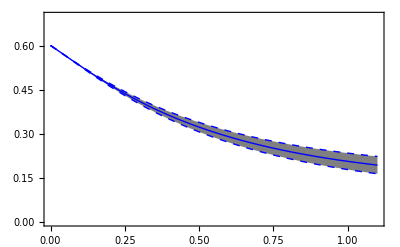

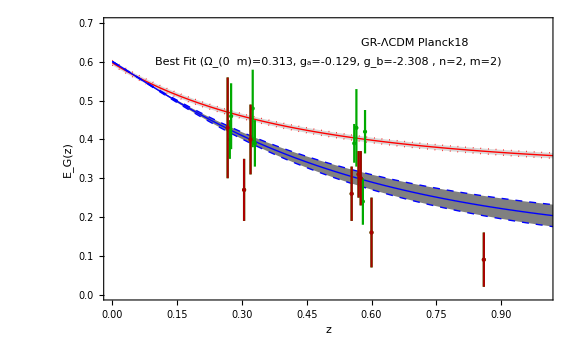

```mathematica
(* Plot Subscript[E, G](z) and best fit on dataset with 1σ deviation *)

pldataeg=ErrorListPlot[dataegb,Frame->True,FrameLabel->{"z","E_G(z)"},BaseStyle->FontSize->16,PlotRange->{{0,1},{0,0.7}},PlotStyle->{PointSize->Large,Darker[Green]},ImageSize->Large]; 
pldataegsub=ErrorListPlot[dataegbsub,Frame->True,FrameLabel->{"z","E_G(z)"},BaseStyle->FontSize->16,PlotRange->{{0,1},{0,0.7}},PlotStyle->{PointSize->Large,Darker[Red]},ImageSize->Large]; 

ploteggr=Plot[  {eg[z,ompl+omplerr,-1,0,0,2,2],eg[z,ompl,-1,0,0,2,2],eg[z,ompl-omplerr,-1,0,0,2,2]},{z,0,1.1},Frame->True,FrameLabel->{"z","E_G(z)"},BaseStyle->FontSize->18,PlotStyle->{{PointSize->Large,Dotted,Thin,Red},{PointSize->Large,Thick,Red},{PointSize->Large,Dotted,Thin,Red}},PlotRange->{{0,1},{0,0.7}},Filling->{{ 1->{{2},LightGray}},{ 2->{{3},LightGray}}},Axes->False,ImageSize->Large];

 
egpar={om,ga,gb};

weg[z_,om_,ga_,gb_]:=eg[z,om,-1,ga,gb,2,2];

deg[z_,om_,ga_,gb_,k_]:=D[weg[z,om,ga,gb],egpar[[k]]];
seg[z_,om_,ga_,gb_,cijs_]:= √(Sum[deg[z,om,ga,gb,i]^2  cijs[[i,i]],{i,1,Length[egpar]}]+2Sum[deg[z,om,ga,gb,i]  deg[z,om,ga,gb,j]  cijs[[i,j]],{i,1,Length[egpar]},{j,i+1,Length[egpar]}]);
cijs={{egs1om^2,egs1om  egs1ga,egs1om egs1gb},{egs1om egs1ga,egs1ga^2,egs1ga  egs1gb},{egs1om  egs1gb,egs1ga  egs1gb,egs1gb^2}}
egbf=weg[z,om,ga,gb]/.chi2mineg[[2]];
egbfs1=(weg[z,om,ga,gb]+seg[z,om,ga,gb,cijs])/.chi2mineg[[2]];
egbfs2=(weg[z,om,ga,gb]-seg[z,om,ga,gb,cijs])/.chi2mineg[[2]];

ParallelEvaluate[Off[InterpolatingFunction::dmvalD];];Off[InterpolatingFunction::dmval];
plegbfs=Plot[{egbfs1,egbf,egbfs2},{z,0,1.1},PlotRange->{{0,1.1},{0,0.7}},Filling->{{ 1->{{2},Gray}},{ 2->{{3},Gray}}},Frame->True,PlotStyle->{{PointSize->Large,Dashed,Thin,Blue},{PointSize->Large,Thick,Blue},{PointSize->Large,Dashed,Thin,Blue}},Axes->False]
figegzbfs=Show[ploteggr,plegbfs,pldataeg,pldataegsub,Graphics[{Inset[" GR-ΛCDM Planck18",{0.7,0.65},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",16}]}],Graphics[{Inset[" Best Fit (Ω_(0  m)=0.313, g_a=-0.129, g_b=-2.308 , n=2, m=2) ",{0.5,0.6},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",16}]}],PlotRange->{{0,1},{0,0.7}},FrameLabel->{"z","E_G(z)"},BaseStyle->{FontFamily->"Times",16},FrameStyle->Directive[Black,Thick],ImageSize->Large]
Export[NotebookDirectory[]<>"figegzbfssub.pdf",figegzbfs,ImageResolution->1000];
```

## Figure 4

```mathematica
(* Tension level in  2D projected space  (Subscript[g, a], Subscript[g, b]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b])   *)

dchieggagb=chi2eg[dataeg,-1,chi2mineg[[2,1,2]],0,0,2,2]-chi2mineg[[1]];
nsigeggagb[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,4}][[1,2]];
nsigeggagb[dchieggagb,3]
```

4.45136

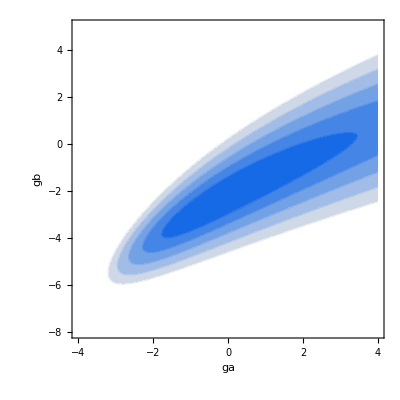

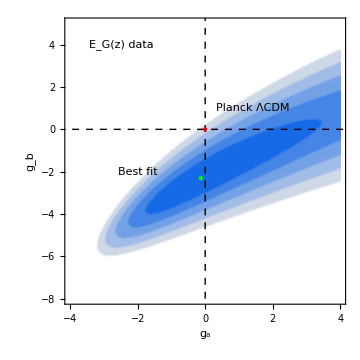

```mathematica
(* 1σ-5σ confidence contour in 2D projected space  (Subscript[g, a], Subscript[g, b]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b]) *)


contour1eg=ContourPlot[chi2eg[dataeg,-1,chi2mineg[[2,1,2]],ga,gb,2,2],{ga,-4,4},{gb,-8,5},FrameLabel->{"ga","gb"},Contours->{chi2mineg[[1]]+dchi[1,3],chi2mineg[[1]]+dchi[2,3],chi2mineg[[1]]+dchi[3,3],chi2mineg[[1]]+dchi[4,3],chi2mineg[[1]]+dchi[5,3]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.1,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.1,.9],White}]



cont1eg=Show[contour1eg,Graphics[{Inset["Best fit",{-2,-2},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["E_G(z) data ",{-2.5,4},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{1.4,1},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"g_a","g_b"},PlotRange->{{-4,4},{-8,5}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{0,-8},{0,20}}]},{Dashed,Line[{{-6,0},{20,0}}]},{PointSize[Large],Red,Point[{0,0}]},{PointSize[Large],Green,Point[{chi2mineg[[2,2,2]],chi2mineg[[2,3,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

```mathematica
(* Tension level in  2D projected space  (Subscript[Ω, 0m], Subscript[g, a]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b])  *)

dchiegomga=chi2eg[dataeg,-1,ompl,0,chi2mineg[[2,3,2]],2,2]-chi2mineg[[1]];
nsigegomga[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,0.01}][[1,2]]
nsigegomga[dchiegomga,3]
```

0.00245873

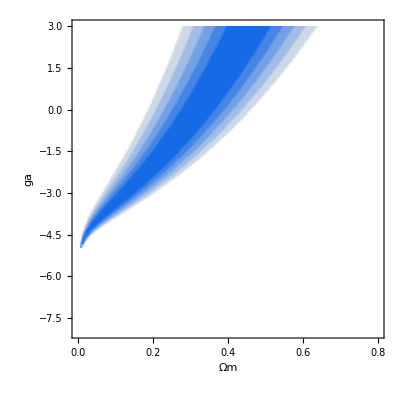

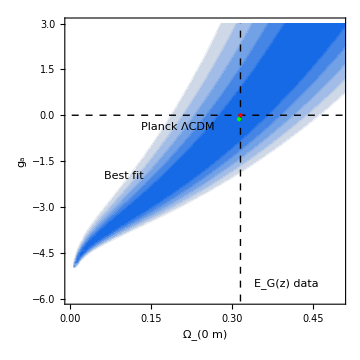

```mathematica
(* 1σ-5σ confidence contour in 2D projected space  (Subscript[Ω, 0m], Subscript[g, a]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b]) *)

contour2eg=ContourPlot[chi2eg[dataeg,-1,om,ga,chi2mineg[[2,3,2]],2,2],{om,0,0.8},{ga,-8,3},FrameLabel->{"Ωm","ga"},Contours->{chi2mineg[[1]]+dchi[1,3],chi2mineg[[1]]+dchi[2,3],chi2mineg[[1]]+dchi[3,3],chi2mineg[[1]]+dchi[4,3],chi2mineg[[1]]+dchi[5,3]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.1,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.1,.9],White}]


cont2eg=Show[contour2eg,Graphics[{Inset["Best fit",{0.1,-2},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["E_G(z) data ",{0.4,-5.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.2,-0.4},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","g_a"},PlotRange->{{0,0.5},{-6,3}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{0.3153,-7},{0.3153,3}}]},{Dashed,Line[{{-0.1,0},{0.6,0}}]},{PointSize[Large],Red,Point[{0.3153,0}]},{PointSize[Large],Green,Point[{chi2mineg[[2,1,2]],chi2mineg[[2,2,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

```mathematica
(* Tension level in  2D projected space  (Subscript[Ω, 0m], Subscript[g, b]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b])   *)

dchiegomgb=chi2eg[dataeg,-1,ompl,chi2mineg[[2,2,2]],0,2,2]-chi2mineg[[1]];
nsigegomgb[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,5}][[1,2]]
nsigegomgb[dchiegomgb,3]
```

4.93638

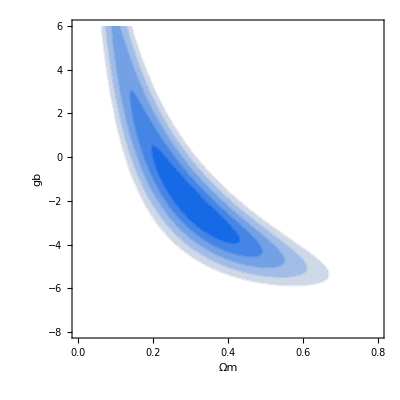

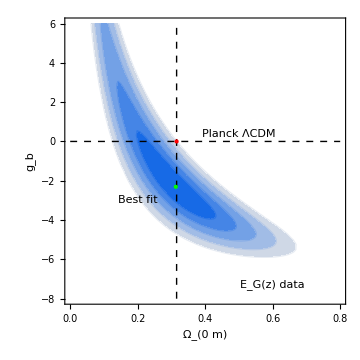

```mathematica
(* 1σ-5σ confidence contour in 2D projected space  (Subscript[Ω, 0m], Subscript[g, b]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b]) *)

contour3eg=ContourPlot[chi2eg[dataeg,-1,om,chi2mineg[[2,2,2]],gb,2,2],{om,0,0.8},{gb,-8,6},FrameLabel->{"Ωm","gb"},Contours->{chi2mineg[[1]]+dchi[1,3],chi2mineg[[1]]+dchi[2,3],chi2mineg[[1]]+dchi[3,3],chi2mineg[[1]]+dchi[4,3],chi2mineg[[1]]+dchi[5,3]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.1,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.1,.9],White}]


cont3eg=Show[contour3eg,Graphics[{Inset["Best fit",{0.2,-3},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["E_G(z) data ",{0.6,-7.3},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.5,0.4},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","g_b"},PlotRange->{{0,0.8},{-8,6}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{0.3153,-8},{0.3153,6}}]},{Dashed,Line[{{0,0},{0.8,0}}]},{PointSize[Large],Red,Point[{0.3153,0}]},{PointSize[Large],Green,Point[{chi2mineg[[2,1,2]],chi2mineg[[2,3,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

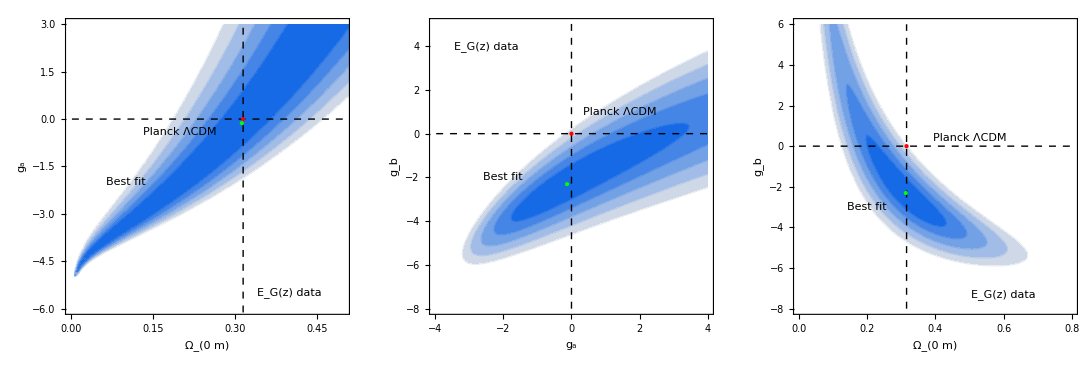

```mathematica
(* The three 1σ-5σ confidence contours in 2D projected spaces of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b]) *)

figeg=GraphicsGrid[{{cont2eg,cont1eg,cont3eg}},Spacings->0]
Export[NotebookDirectory[]<>"contEgtensionb.pdf",figeg,ImageResolution->1000];
```

## Figure 5

```mathematica
(* Covariance Matrix for data  fσ8*)


Cijwigglez=10^-3*({{6.400, 2.570, 0.000}, {2.570, 3.969, 2.540}, {0.000, 2.540, 5.184}});

Wigglez={10,11,12};
Cijf=DiagonalMatrix[datafσ8fid[[All,3]]^2];
Cijf[[Wigglez,Wigglez]]=Cijwigglez;
InvCijf=Inverse[Cijf];

Cijf//MatrixForm;
(* Covariance Matrix for data  Eg*)

Cije=DiagonalMatrix[dataeg[[All,3]]^2];

InvCije=Inverse[Cije];

Cije//MatrixForm;
```

```mathematica
(* Correlated χ^2 term for Eg*)
 
vec1[data1_,w_,om_,ga_,gb_,n_,m_]:=Table[(data1[[i,2]]-eg[data1[[i,1]],om,w,ga,gb,n,m]),{i,1,Length[data1]}];
chi2e[data1_,w_,om_,ga_,gb_,n_,m_]:=vec1[data1,w,om,ga,gb,n,m].InvCije.vec1[data1,w,om,ga,gb,n,m]


(* Correlated χ^2 term for fσ8 with fiducial cosmology *)
vec2[data2_,w_,om_,ga_,n_,σ8_]:=Table[data2[[j,2]]-ratio1[data2[[j,1]],w,om,data2[[j,4]]]fσ8geff[1/(1+data2[[j,1]]),om,w,ga,n,σ8],{j,1,Length[data2]}]
chi2f[data2_,w_,om_,ga_,n_,σ8_]:=vec2[data2,w,om,ga,n,σ8].InvCijf.vec2[data2,w,om,ga,n,σ8]


(* Correlated χ^2 term for fσ8 without fiducial cosmology *)

vec2nofid[data2_,w_,om_,ga_,n_,σ8_]:=Table[data2[[j,2]]-fσ8geff[1/(1+data2[[j,1]]),om,w,ga,n,σ8],{j,1,Length[data2]}]
chi2fnofid[data2_,w_,om_,ga_,n_,σ8_]:=vec2nofid[data2,w,om,ga,n,σ8].InvCijf.vec2nofid[data2,w,om,ga,n,σ8]


(* Correlated χ^2 term for Eg  and fσ8 with fiducial cosmology *)

chi2[data1_,data2_,w_,om_,ga_,gb_,n_,m_,σ8_]:=chi2f[data2,w,om,ga,n,σ8]+chi2e[data1,w,om,ga,gb,n,m]


(* Correlated χ^2 term for Eg  and fσ8 without fiducial cosmology *)

chi2allnofid[data1_,data2_,w_,om_,ga_,gb_,n_,m_,σ8_]:=chi2fnofid[data2,w,om,ga,n,σ8]+chi2e[data1,w,om,ga,gb,n,m]
```

```mathematica
(* Minimization of χ^2 for data with fiducial cosmology *)

chi2min=FindMinimum[chi2[dataeg,datafσ8fid,-1,om,ga,gb,2,2,σ8],{om,0.3,0.31},{ga,0,-0.1},{gb,0,-0.1},{σ8,0.81,0.82}]

(* Minimization of χ^2 for data with fiducial cosmology *)

chi2minallnofid=FindMinimum[chi2allnofid[dataeg,datafσ8,-1,om,ga,gb,2,2,σ8],{om,0.3,0.31},{ga,0,-0.1},{gb,0,-0.1},{σ8,0.81,0.82}]
```

{53.1915,{om→0.274655,ga→-0.956668,gb→-2.44838,σ8→0.848348}}

{53.3176,{om→0.263564,ga→-1.11517,gb→-2.42191,σ8→0.878697}}

```mathematica
(* Tension level in the  3D parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) with fiducial cosmology *)

dchigagbomσ8=chi2[dataeg,datafσ8fid,-1,ompl,0,0,2,2,σ8pl]-chi2min[[1]];
nsiggagbomσ8[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,6},AccuracyGoal->2][[1,2]]
nsiggagbomσ8[dchigagbomσ8,4]

(* Tension level in the  3D parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) without fiducial cosmology *)

dchiallnofidgagbomσ8=chi2allnofid[dataeg,datafσ8,-1,ompl,0,0,2,2,σ8pl]-chi2minallnofid[[1]];
nsigallnofidgagbomσ8[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,6},AccuracyGoal->2][[1,2]]
nsigallnofidgagbomσ8[dchiallnofidgagbomσ8,4]
```

6.03424

6.33378

```mathematica
(* 1σ  standard deviations with fiducial cosmology*)

s1om=FindRoot[chi2[dataeg,datafσ8fid,-1,om,chi2min[[2,2,2]],chi2min[[2,3,2]],2,2,chi2min[[2,4,2]]]==chi2min[[1]]+1,{om,chi2min[[2,1,2]]+0.5}][[1,2]]-chi2min[[2,1,2]];
s1ga=FindRoot[chi2[dataeg,datafσ8fid,-1,chi2min[[2,1,2]],ga,chi2min[[2,3,2]],2,2,chi2min[[2,4,2]]]==chi2min[[1]]+1,{ga,chi2min[[2,2,2]]+0.5}][[1,2]]-chi2min[[2,2,2]];
s1gb=FindRoot[chi2[dataeg,datafσ8fid,-1,chi2min[[2,1,2]],chi2min[[2,2,2]],gb,2,2,chi2min[[2,4,2]]]==chi2min[[1]]+1,{gb,chi2min[[2,3,2]]+0.5}][[1,2]]-chi2min[[2,3,2]];
s1σ8=FindRoot[chi2[dataeg,datafσ8fid,-1,chi2min[[2,1,2]],chi2min[[2,2,2]],chi2min[[2,3,2]],2,2,σ8]==chi2min[[1]]+1,{σ8,chi2min[[2,4,2]]+0.5}][[1,2]]-chi2min[[2,4,2]];

Print["1σ Ωm=",s1om]
Print["1σ ga=",s1ga]
Print["1σ gb=",s1gb]
Print["1σ σ8=",s1σ8]
```

1σ Ωm=0.014504

1σ ga=0.144479

1σ gb=0.414339

1σ σ8=0.0147844

```mathematica
(* 1σ  standard deviations without fiducial cosmology*)

allnofids1om=FindRoot[chi2allnofid[dataeg,datafσ8,-1,om,chi2minallnofid[[2,2,2]],chi2minallnofid[[2,3,2]],2,2,chi2minallnofid[[2,4,2]]]==chi2minallnofid[[1]]+1,{om,chi2minallnofid[[2,1,2]]+0.5}][[1,2]]-chi2minallnofid[[2,1,2]];
allnofids1ga=FindRoot[chi2allnofid[dataeg,datafσ8,-1,chi2minallnofid[[2,1,2]],ga,chi2minallnofid[[2,3,2]],2,2,chi2minallnofid[[2,4,2]]]==chi2minallnofid[[1]]+1,{ga,chi2minallnofid[[2,2,2]]+0.5}][[1,2]]-chi2minallnofid[[2,2,2]];
allnofids1gb=FindRoot[chi2allnofid[dataeg,datafσ8,-1,chi2minallnofid[[2,1,2]],chi2minallnofid[[2,2,2]],gb,2,2,chi2minallnofid[[2,4,2]]]==chi2minallnofid[[1]]+1,{gb,chi2minallnofid[[2,3,2]]+0.5}][[1,2]]-chi2minallnofid[[2,3,2]];
allnofids1σ8=FindRoot[chi2allnofid[dataeg,datafσ8,-1,chi2minallnofid[[2,1,2]],chi2minallnofid[[2,2,2]],chi2minallnofid[[2,3,2]],2,2,σ8]==chi2minallnofid[[1]]+1,{σ8,chi2minallnofid[[2,4,2]]+0.5}][[1,2]]-chi2minallnofid[[2,4,2]];

Print["1σ Ωm=",allnofids1om]
Print["1σ ga=",allnofids1ga]
Print["1σ gb=",allnofids1gb]
Print["1σ σ8=",allnofids1σ8]
```

1σ Ωm=0.0123216

1σ ga=0.136676

1σ gb=0.415931

1σ σ8=0.0153065

```mathematica
(* Tension level in  2D projected space  (Subscript[g, a], Subscript[g, b]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) with fiducial cosmology *)

dchigagb=chi2[dataeg,datafσ8fid,-1,chi2min[[2,1,2]],0,0,2,2,chi2min[[2,4,2]]]-chi2min[[1]];
nsiggagb[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,6},AccuracyGoal->4,PrecisionGoal->4][[1,2]]
nsiggagb[dchigagb,4]
```

5.74377

```mathematica
(* Tension level in  2D projected space  (Subscript[g, a], Subscript[g, b]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) without fiducial cosmology *)

dchiallnofidgagb=chi2allnofid[dataeg,datafσ8,-1,chi2min[[2,1,2]],0,0,2,2,chi2minallnofid[[2,4,2]]]-chi2minallnofid[[1]];
nsigallnofidgagb[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,8},AccuracyGoal->1,PrecisionGoal->1][[1,2]]
nsigallnofidgagb[dchiallnofidgagb,4]
```

7.52765

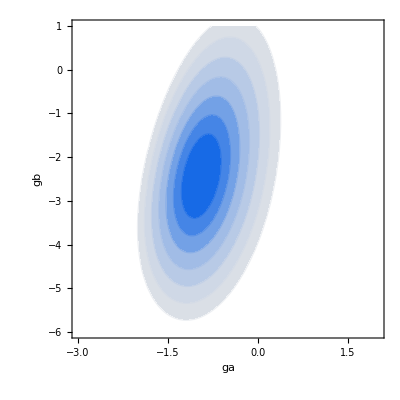

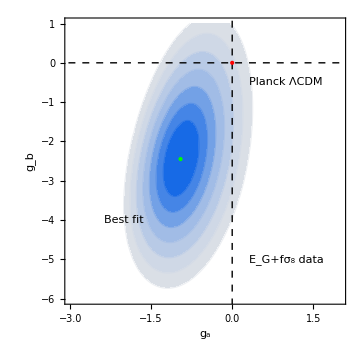

```mathematica
(* 1σ-7σ confidence contour in 2D projected space  (Subscript[g, a], Subscript[g, b]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) including the fiducial correction factor*)

contour1=ContourPlot[chi2[dataeg,datafσ8fid,-1,chi2min[[2,1,2]],ga,gb,2,2,chi2min[[2,4,2]]],{ga,-3,2},{gb,-6,1},FrameLabel->{"ga","gb"},Contours->{chi2min[[1]]+dchi[1,4],chi2min[[1]]+dchi[2,4],chi2min[[1]]+dchi[3,4],chi2min[[1]]+dchi[4,4],chi2min[[1]]+dchi[5,4],chi2min[[1]]+dchi[6,4],chi2min[[1]]+dchi[7,4]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White}]


cont=Show[contour1,Graphics[{Inset["Best fit",{-2,-4},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["E_G+fσ_8 data ",{1,-5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{1,-0.5},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"g_a","g_b"},PlotRange->{{-3,2},{-6,1}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{0,-10},{0,10}}]},{Dashed,Line[{{-5,0},{15,0}}]},{PointSize[Large],Red,Point[{0,0}]},{PointSize[Large],Green,Point[{chi2min[[2,2,2]],chi2min[[2,3,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

```mathematica
(* Tension level in  2D projected space  (Subscript[Ω, 0m], Subscript[g, a]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) with fiducial cosmology *)

dchiomga=chi2[dataeg,datafσ8fid,-1,ompl,0,chi2min[[2,3,2]],2,2,chi2min[[2,4,2]]]-chi2min[[1]];
nsigomga[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,6},AccuracyGoal->2][[1,2]]
nsigomga[dchiomga,4]
```

6.38933

```mathematica
(* Tension level in  2D projected space  (Subscript[Ω, 0m], Subscript[g, a]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) without fiducial cosmology *)

dchiallnofidomga=chi2allnofid[dataeg,datafσ8,-1,ompl,0,chi2minallnofid[[2,3,2]],2,2,chi2minallnofid[[2,4,2]]]-chi2minallnofid[[1]];
nsigallnofidomga[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,8},AccuracyGoal->2][[1,2]]

If[dchiallnofidomga<79,nsigallnofidomga[dchiallnofidomga,4],nsigallnofidomga>8.2]
```

nsigallnofidomga>8.2

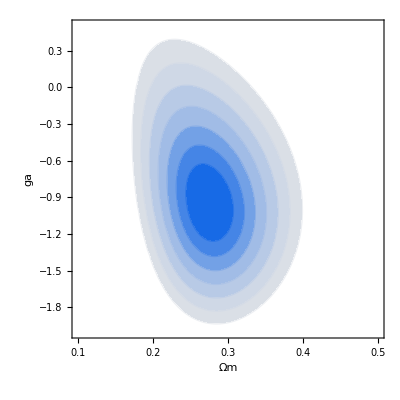

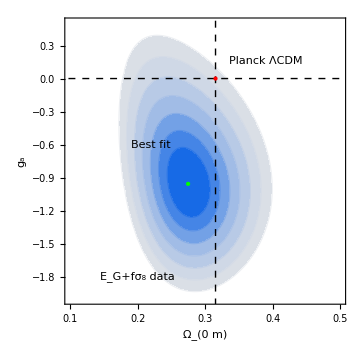

```mathematica
(* 1σ-7σ confidence contour in 2D projected space  (Subscript[Ω, 0m], Subscript[g, a]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) including the fiducial correction factor *)

contour2=ContourPlot[chi2[dataeg,datafσ8fid,-1,om,ga,chi2min[[2,3,2]],2,2,chi2min[[2,4,2]]],{om,0.1,0.5},{ga,-2,0.5},FrameLabel->{"Ωm","ga"},Contours->{chi2min[[1]]+dchi[1,4],chi2min[[1]]+dchi[2,4],chi2min[[1]]+dchi[3,4],chi2min[[1]]+dchi[4,4],chi2min[[1]]+dchi[5,4],chi2min[[1]]+dchi[6,4],chi2min[[1]]+dchi[7,4]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White}]


cont2=Show[contour2,Graphics[{Inset["Best fit",{0.22,-0.6},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["E_G+fσ_8 data ",{0.2,-1.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.39,0.16},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","g_a"},PlotRange->{{0.1,0.5},{-2,0.5}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{0.3153,-6},{0.3153,2}}]},{Dashed,Line[{{-0.1,0},{1,0}}]},{PointSize[Large],Red,Point[{0.3153,0}]},{PointSize[Large],Green,Point[{chi2min[[2,1,2]],chi2min[[2,2,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

```mathematica
(* Tension level in  2D projected space  (Subscript[Ω, 0m], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) with fiducial cosmology *)

dchioms8=chi2[dataeg,datafσ8fid,-1,ompl,chi2min[[2,2,2]],chi2min[[2,3,2]],2,2,σ8pl]-chi2min[[1]];

nsigoms8[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2},AccuracyGoal->2][[1,2]]
nsigoms8[dchioms8,4]
```

1.4662

```mathematica
(* Tension level in  2D projected space  (Subscript[Ω, 0m], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) without fiducial cosmology *)

dchiallnofidoms8=chi2allnofid[dataeg,datafσ8,-1,ompl,chi2minallnofid[[2,2,2]],chi2min[[2,3,2]],2,2,σ8pl]-chi2minallnofid[[1]];

nsigallnofidoms8[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2},AccuracyGoal->2][[1,2]]
nsigallnofidoms8[dchiallnofidoms8,4]
```

2.1697

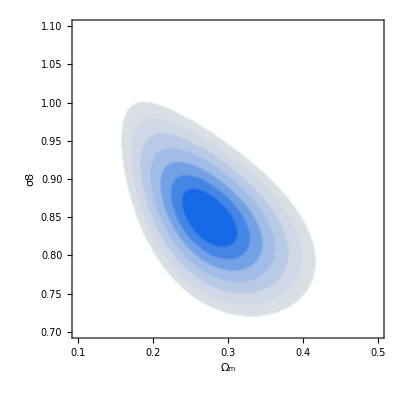

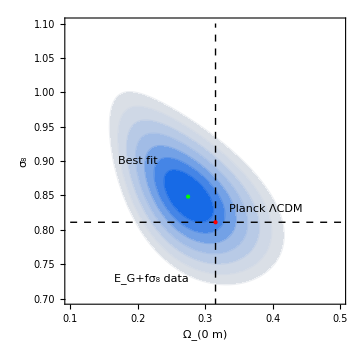

```mathematica
(* 1σ-7σ confidence contour in 2D projected space  (Subscript[Ω, 0m], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) including the fiducial correction factor*)

contour3=ContourPlot[chi2[dataeg,datafσ8fid,-1,om,chi2min[[2,2,2]],chi2min[[2,3,2]],2,2,σ8],{om,0.1,0.5},{σ8,0.7,1.1},FrameLabel->{"Ω_m","σ8"},Contours->{chi2min[[1]]+dchi[1,4],chi2min[[1]]+dchi[2,4],chi2min[[1]]+dchi[3,4],chi2min[[1]]+dchi[4,4],chi2min[[1]]+dchi[5,4],chi2min[[1]]+dchi[6,4],chi2min[[1]]+dchi[7,4]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White}]


cont3=Show[contour3,Graphics[{Inset["Best fit",{0.2,0.9},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["E_G+fσ_8 data ",{0.22,0.73},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.39,0.83},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0.1,0.5},{0.7,1.1}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{0.3153,0.6},{0.3153,1.1}}]},{Dashed,Line[{{0.1,0.8111},{0.6,0.8111}}]},{PointSize[Large],Red,Point[{0.3153,0.8111}]},{PointSize[Large],Green,Point[{chi2min[[2,1,2]],chi2min[[2,4,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

```mathematica
(* Tension level in  2D projected space  (Subscript[Ω, 0m], Subscript[g, b]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) with fiducial cosmology *)

dchiomgb=chi2[dataeg,datafσ8fid,-1,ompl,chi2min[[2,2,2]],0,2,2,chi2min[[2,4,2]]]-chi2min[[1]];
nsigomgb[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,7},AccuracyGoal->1][[1,2]]
nsigomgb[dchiomgb,4]
```

7.73849

```mathematica
(* Tension level in  2D projected space  (Subscript[Ω, 0m], Subscript[g, b]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) without fiducial cosmology *)

dchiallnofidomgb=chi2allnofid[dataeg,datafσ8,-1,ompl,chi2minallnofid[[2,2,2]],0,2,2,chi2minallnofid[[2,4,2]]]-chi2minallnofid[[1]];
nsigallnofidomgb[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,8},AccuracyGoal->1][[1,2]]
If[ dchiallnofidomgb<79,nsigallnofidomgb[dchiallnofidomgb,4],nsigallnofidomgb>8.2]
```

nsigallnofidomgb>8.2

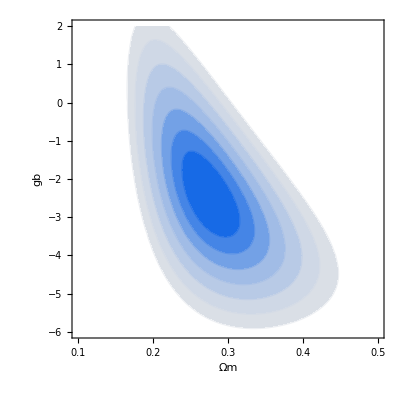

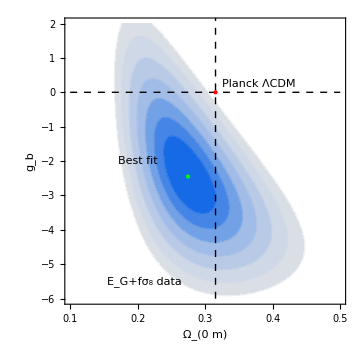

```mathematica
(* 1σ-7σ confidence contour in 2D projected space  (Subscript[Ω, 0m], Subscript[g, b]) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) including the fiducial correction factor*)

contour4=ContourPlot[chi2[dataeg,datafσ8fid,-1,om,chi2min[[2,2,2]],gb,2,2,chi2min[[2,4,2]]],{om,0.1,0.5},{gb,-6,2},FrameLabel->{"Ωm","gb"},Contours->{chi2min[[1]]+dchi[1,4],chi2min[[1]]+dchi[2,4],chi2min[[1]]+dchi[3,4],chi2min[[1]]+dchi[4,4],chi2min[[1]]+dchi[5,4],chi2min[[1]]+dchi[6,4],chi2min[[1]]+dchi[7,4]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White}]


cont4=Show[contour4,Graphics[{Inset["Best fit",{0.2,-2},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["E_G+fσ_8 data  ",{0.21,-5.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.38,0.25},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","g_b"},PlotRange->{{0.1,0.5},{-6,2}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{0.3153,-6},{0.3153,3}}]},{Dashed,Line[{{0.1,0},{0.5,0}}]},{PointSize[Large],Red,Point[{0.3153,0}]},{PointSize[Large],Green,Point[{chi2min[[2,1,2]],chi2min[[2,3,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

```mathematica
(* Tension level in  2D projected space  (Subscript[g, a], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) with fiducial cosmology *)

dchigas8=chi2[dataeg,datafσ8fid,-1,chi2min[[2,1,2]],0,chi2min[[2,3,2]],2,2,σ8pl]-chi2min[[1]];

nsiggas8[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2},AccuracyGoal->2][[1,2]]
nsiggas8[dchigas8,4]
```

2.58907

```mathematica
(* Tension level in  2D projected space  (Subscript[g, a], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) without fiducial cosmology *)

dchiallnofidgas8=chi2allnofid[dataeg,datafσ8,-1,chi2minallnofid[[2,1,2]],0,chi2minallnofid[[2,3,2]],2,2,σ8pl]-chi2minallnofid[[1]];

nsigallnofidgas8[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2},AccuracyGoal->2][[1,2]]
nsigallnofidgas8[dchiallnofidgas8,4]
```

2.16381

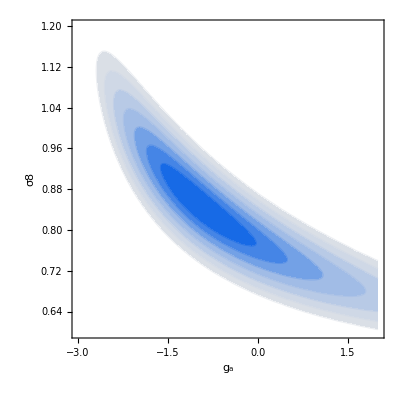

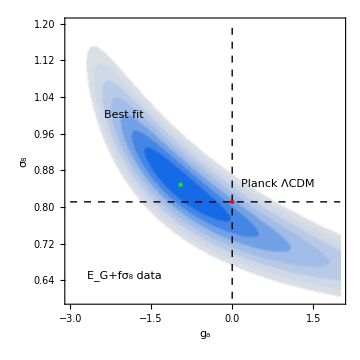

```mathematica
(* 1σ-7σ confidence contour in 2D projected space  (Subscript[g, a], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) including the fiducial correction factor*)

contour5=ContourPlot[chi2[dataeg,datafσ8fid,-1,chi2min[[2,1,2]],ga,chi2min[[2,3,2]],2,2,σ8],{ga,-3,2},{σ8,0.6,1.2},FrameLabel->{"g_a","σ8"},Contours->{chi2min[[1]]+dchi[1,4],chi2min[[1]]+dchi[2,4],chi2min[[1]]+dchi[3,4],chi2min[[1]]+dchi[4,4],chi2min[[1]]+dchi[5,4],chi2min[[1]]+dchi[6,4],chi2min[[1]]+dchi[7,4]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White}]
cont5=Show[contour5,Graphics[{Inset["Best fit",{-2,1},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["E_G+fσ_8 data ",{-2,0.65},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.84,0.85},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"g_a","σ_8"},PlotRange->{{-3,2},{0.6,1.2}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{0,0.6},{0,1.2}}]},{Dashed,Line[{{-3,σ8pl},{2,σ8pl}}]},{PointSize[Large],Red,Point[{0,σ8pl}]},{PointSize[Large],Green,Point[{chi2min[[2,2,2]],chi2min[[2,4,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

```mathematica
(* Tension level in  2D projected space  (Subscript[g, b], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) with fiducial cosmology *)

dchigbs8=chi2[dataeg,datafσ8fid,-1,chi2min[[2,1,2]],chi2min[[2,2,2]],0,2,2,σ8pl]-chi2min[[1]];

nsiggbs8[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,6},AccuracyGoal->2][[1,2]]
nsiggbs8[dchigbs8,4]
```

5.58432

```mathematica
(* Tension level in  2D projected space  (Subscript[g, b], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) without fiducial cosmology *)

dchiallnofidgbs8=chi2allnofid[dataeg,datafσ8,-1,chi2min[[2,1,2]],chi2minallnofid[[2,2,2]],0,2,2,σ8pl]-chi2minallnofid[[1]];

nsigallnofidgbs8[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,8},AccuracyGoal->2][[1,2]]
nsigallnofidgbs8[dchiallnofidgbs8,4]
```

6.74011

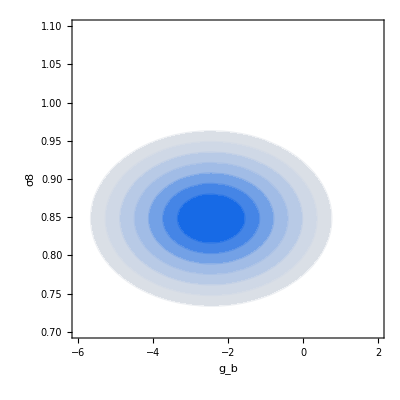

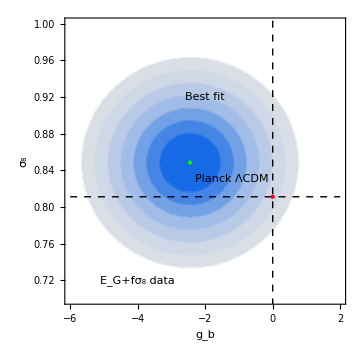

```mathematica
(* 1σ-7σ confidence contour in 2D projected space  (Subscript[g, b], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) including the fiducial correction factor*)

contour6=ContourPlot[chi2[dataeg,datafσ8fid,-1,chi2min[[2,1,2]],chi2min[[2,2,2]],gb,2,2,σ8],{gb,-6,2},{σ8,0.7,1.1},FrameLabel->{"g_b","σ8"},Contours->{chi2min[[1]]+dchi[1,4],chi2min[[1]]+dchi[2,4],chi2min[[1]]+dchi[3,4],chi2min[[1]]+dchi[4,4],chi2min[[1]]+dchi[5,4],chi2min[[1]]+dchi[6,4],chi2min[[1]]+dchi[7,4]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White}]
cont6=Show[contour6,Graphics[{Inset["Best fit",{-2,0.92},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["E_G+fσ_8 data ",{-4,0.72},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{-1.2,0.83},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"g_b","σ_8"},PlotRange->{{-6,2},{0.7,1}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{0,0.6},{0,1.2}}]},{Dashed,Line[{{-6,σ8pl},{2,σ8pl}}]},{PointSize[Large],Red,Point[{0,σ8pl}]},{PointSize[Large],Green,Point[{chi2min[[2,3,2]],chi2min[[2,4,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

```mathematica
(* The six 1σ-7σ confidence contours in 2D projected spaces of the parameter space (Subscript[Ω, 0m], Subscript[g, a], Subscript[g, b], σ8) including the fiducial correction factor*)


fig=GraphicsGrid[{{cont3,cont2,cont5},{cont,cont4,cont6}},Spacings->4]

Export[NotebookDirectory[]<>"egfs8all.pdf",fig,ImageResolution->1000];
```

-Graphics-